```mathematica
l1=0.2356;
l2=0.9719;
l3=4.0818;
a0=1;
a1=-0.2359;
a2=0.08222;
A=Table[0,{x,4},{y,4}];
A[[1,1]]=0;
A[[1,2]]=0;
A[[1,3]]=a0*l1;
A[[1,4]]=a0*l2;
A[[2,1]]=0;
A[[2,2]]=0;
A[[2,3]]=a0*l2;
A[[2,4]]=-a0*l1;
A[[3,1]]=a0*l1;
A[[3,2]]=a0*l2;
A[[3,3]]=-(a1*l1+a2*l2)+a0*l3;
A[[3,4]]=(a2*l1-a1*l2);
A[[4,1]]=a0*l2;
A[[4,2]]=-a0*l1;
A[[4,3]]=(a2*l1-a1*l2);
A[[4,4]]=(a1*l1+a2*l2)+a0*l3;
A
```

{{0,0,0.2356,0.9719},{0,0,0.9719,-0.2356},{0.2356,0.9719,4.05747,0.248642},{0.9719,-0.2356,0.248642,4.10613}}

```mathematica
q1=0
q2=2*a0*l1
q3=2*a0*l2
q4=0
q5=0
q6=-2*a1*l2+2*a2*l1
q7=-a1*l1-a2*l2
q8=a0*l3
```

0

0.4712

1.9438

0

0

0.497284

-0.0243316

4.0818

```mathematica
l1=0.9287;
l2=-0.3709;
l3=4.2042;
a0=1;
a1=4.1389;
a2=0.2095;
B=Table[0,{x,4},{y,4}];
B[[1,1]]=0;
B[[1,2]]=0;
B[[1,3]]=a0*l1;
B[[1,4]]=a0*l2;
B[[2,1]]=0;
B[[2,2]]=0;
B[[2,3]]=a0*l2;
B[[2,4]]=-a0*l1;
B[[3,1]]=a0*l1;
B[[3,2]]=a0*l2;
B[[3,3]]=-(a1*l1+a2*l2)+a0*l3;
B[[3,4]]=(a2*l1-a1*l2);
B[[4,1]]=a0*l2;
B[[4,2]]=-a0*l1;
B[[4,3]]=(a2*l1-a1*l2);
B[[4,4]]=(a1*l1+a2*l2)+a0*l3;
B
```

{{0,0,0.9287,-0.3709},{0,0,-0.3709,-0.9287},{0.9287,-0.3709,0.438107,1.72968},{-0.3709,-0.9287,1.72968,7.97029}}

```mathematica
q1=0
q2=2*a0*l1
q3=2*a0*l2
q4=0
q5=0
q6=-2*a1*l2+2*a2*l1
q7=-a1*l1-a2*l2
q8=a0*l3
```

0

1.8574

-0.7418

0

0

3.45936

-3.76609

4.2042

```mathematica
myplot=ContourPlot3D[{A[[1, 1]]*x^2 + (A[[1, 2]] + A[[2, 1]])*x*y + (A[[1, 3]] + A[[3, 1]])*x*z + (A[[1, 4]] + A[[4, 1]])*x + A[[2, 2]]*y^2 + (A[[2, 3]] + A[[3, 2]])*y*z + (A[[2, 4]] + A[[4, 2]])*y + A[[3, 3]]*z^2 + (A[[3, 4]] + A[[4, 3]])*z + A[[4, 4]] == 0, B[[1, 1]]*x^2 + (B[[1, 2]] + B[[2, 1]])*x*y + (B[[1, 3]] + B[[3, 1]])*x*z + (B[[1, 4]] + B[[4, 1]])*x + B[[2, 2]]*y^2 + (B[[2, 3]] + B[[3, 2]])*y*z + (B[[2, 4]] + B[[4, 2]])*y + B[[3, 3]]*z^2 + (B[[3, 4]] + B[[4, 3]])*z + B[[4, 4]] == 0}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, PerformanceGoal -> "Quality", MeshStyle -> Gray, Mesh -> 0, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}, MaxRecursion -> 15, PlotPoints -> 50, PlotRange -> Automatic, ContourStyle -> {{Orange, Opacity[0.5]}, {Magenta,Opacity[0.5]}}];
Show[myplot]
```

-Graphics3D-

```mathematica
eigenvalues=Eigenvalues[A];
eigenvectors=Eigenvectors[A];
transformatrix=Transpose[{eigenvectors[[1]],eigenvectors[[2]],eigenvectors[[3]], eigenvectors[[4]]}];
```

```mathematica
afterA=Transpose[transformatrix].A.transformatrix;
MatrixForm[afterA]
```

(4.55137 | -8.88178×10^-16 | 4.44089×10^-16 | -5.55112×10^-16
-8.88178×10^-16 | 4.07726 | 1.4988×10^-15 | -1.22125×10^-15
3.05311×10^-16 | 1.47105×10^-15 | -0.245287 | -2.02876×10^-15
-3.98986×10^-16 | -1.19696×10^-15 | -1.9906×10^-15 | -0.219736)

```mathematica
afterB=Transpose[transformatrix].B.transformatrix;
MatrixForm[afterB]
```

(5.94326 | 3.41967 | -0.156775 | -1.44755
3.41967 | 1.93033 | 0.61513 | -1.73576
-0.156775 | 0.61513 | 0.185624 | -0.206996
-1.44755 | -1.73576 | -0.206996 | 0.349191)

```mathematica
Clear[V];Clear[u];Clear[v];
V={(u+afterA[[1,1]]*v)/afterA[[1,1]], (u*v-afterA[[2,2]])/afterA[[2,2]], (u-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
goalformula=Collect[Expand[V.afterB.V], {u^2, u}]
```

23.3636-6.32906 v+10.7382 v^2+u (-7.09488+3.32952 v-0.796929 v^2)+u^2 (0.387977-0.431847 v-0.393661 v^2)

```mathematica
delta=Expand[(-7.094883388176753+3.3295203884935534 v-0.7969288593623463 v^2)^2-4*(0.3879770955987426-0.43184746085518355 v-0.39366074546109425 v^2)*(23.363569163491753-6.329056267204264 v+10.738201368648564 v^2)];
```

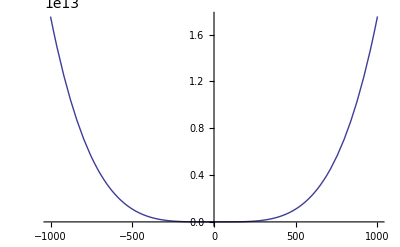

```mathematica
Plot[delta, {v,-1000, 1000}]
```

```mathematica
Solve[delta==0, v]
```

{{v→-0.0466868-0.945332 ⅈ},{v→-0.0466868+0.945332 ⅈ},{v→-0.0466867-0.945332 ⅈ},{v→-0.0466867+0.945332 ⅈ}}

```mathematica
u1=(-(-7.094883388176753+3.3295203884935534 v-0.7969288593623463 v^2)+Sqrt[delta])/(2*(0.3879770955987426-0.43184746085518355 v-0.39366074546109425 v^2));
u2=(-(-7.094883388176753+3.3295203884935534 v-0.7969288593623463 v^2)-Sqrt[delta])/(2*(0.3879770955987426-0.43184746085518355 v-0.39366074546109425 v^2));
```

```mathematica
afterP1={(u1+afterA[[1,1]]*v)/afterA[[1,1]], (u1*v-afterA[[2,2]])/afterA[[2,2]], (u1-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u1*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
afterP2={(u2+afterA[[1,1]]*v)/afterA[[1,1]], (u2*v-afterA[[2,2]])/afterA[[2,2]], (u2-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u2*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
P1=transformatrix.afterP1;
P2=transformatrix.afterP2;
```

```mathematica
Branch1=Graphics3D[{PointSize[0.01],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-7, 1, 0.005}]]}, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}];
Branch2=Graphics3D[{PointSize[0.01],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,1, 4.2, 0.01}]]}];
Show[Branch1,Branch2,myplot]
```

-Graphics3D-